### Number state

```mathematica
Clear[Q];
Q[α_,n_] := 1/π Exp[-Abs[α]^2]((Abs[α]^2)^n)/(n!)
```

```mathematica
pr=5;
Plot3D[Q[x+ⅈ y,3],{x,-pr,pr},{y,-pr,pr},
PlotRange->All,
PlotPoints->50]
```

-Graphics3D-

### Coherent mixture of number states

```mathematica
Clear[Q];
Q[α_,n_] := 1/π Exp[-Abs[α]^2]((Abs[α]^2)^n)/(n!)Abs[1/(√2)+Conjugate[α]/(√2 √(n+1))]^2;
```

```mathematica
NIntegrate[Q[x+ⅈ y,3],{x,-∞,∞},{y,-∞,∞}]
```

1.

```mathematica
pr=5;
p1=Plot3D[Q[x+ⅈ y,3],{x,-pr,pr},{y,-pr,pr},
PlotRange->All,
PlotPoints->50,
PlotLabel->Style["Coherent mixture",Black,20]]
```

-Graphics3D-

### Incoherent mixture of number states

```mathematica
Clear[Q];
Q[α_,n_] := 1/π Exp[-Abs[α]^2]((Abs[α]^2)^n)/(n!)(1/2+Abs[α]^2/(2(n+1)));
```

```mathematica
NIntegrate[Q[x+ⅈ y,3],{x,-∞,∞},{y,-∞,∞}]
```

1.

```mathematica
pr=5;
p2=Plot3D[Q[x+ⅈ y,3],{x,-pr,pr},{y,-pr,pr},
PlotRange->All,
PlotPoints->50,
PlotLabel->Style["Incoherent mixture",Black,20]]
```

-Graphics3D-

```mathematica
grid[{p1,p2}]
```

-Graphics3D- | -Graphics3D-

### Useful calculations to knkow

```mathematica
u = (x+ⅈ y)/2;
α = (a+ⅈ b);
u* α - u α*//cf
```

ⅈ (b x-a y)

```mathematica
Simplify/@%
```

-ⅈ ui x-x (ur-ⅈ vi+vr-2 ⅈ αi)-y (ui-ⅈ ur+vi+ⅈ vr+2 ⅈ αr)

```mathematica
Integrate[Exp[-1/2 λ λ* + λ α* - λ* α],{λr,-∞,∞},{λi,-∞,∞},Assumptions->{αr∈Reals,αi∈Reals}]
```

2 ⅇ^(-2 (αi^2+αr^2)) π

```mathematica
Integrate[Exp[-1/2 λ λ* + λ α* + λ* α],{λr,-∞,∞},{λi,-∞,∞},Assumptions->{αr∈Reals,αi∈Reals}]
```

2 ⅇ^(2 (αi^2+αr^2)) π

```mathematica
Integrate[Exp[-1/2 λ λ* + λ (α-β)* + λ* (α+β)],{λr,-∞,∞},{λi,-∞,∞},Assumptions->{αr∈Reals,αi∈Reals,βr∈Reals,βi∈Reals}]//cf
```

2 ⅇ^(2 ((αr+ⅈ βi)^2+(αi-ⅈ βr)^2)) π

```mathematica
Integrate[Exp[-1/2 λ λ* - λ (α+β)* - λ* (α-β)],{λr,-∞,∞},{λi,-∞,∞},Assumptions->{αr∈Reals,αi∈Reals,βr∈Reals,βi∈Reals}]//cf
```

2 ⅇ^(2 (αi-ⅈ αr-βi+ⅈ βr) (αi+ⅈ αr+βi+ⅈ βr)) π

```mathematica
Integrate[Exp[-1/2 λ λ* + λ α* - λ*  β],{λr,-∞,∞},{λi,-∞,∞},Assumptions->{αr∈Reals,αi∈Reals,βr∈Reals,βi∈Reals}]//cf
```

2 ⅇ^(-2 (αi+ⅈ αr) (βi-ⅈ βr)) π

```mathematica
Integrate[Exp[-x^2/a+ⅈ k x],{x,-∞,∞},Assumptions->{k>0,a>0}]
```

√a ⅇ^(-(a k^2)/4) √π

### Cat states

```mathematica
α = (αr + ⅈ αi);
β = βr + ⅈ βi;
W = 1/(π(1+Exp[-2α α*]))(Exp[-2(α-β)(α-β)*]+ Exp[-2(α+β)(α+β)*]+Exp[-2 α α*](Exp[2(α-β)*(α+β)]+Exp[2(α-β)(α+β)*]))//ComplexExpand//FullSimplify
```

(ⅇ^(-2 (2 αi βi+βi^2+βr (2 αr+βr))) (1+ⅇ^(8 αi βi+8 αr βr)+2 ⅇ^(2 (αi^2+2 αi βi+αr (αr+2 βr))) Cos[4 αr βi-4 αi βr]))/((1+ⅇ^(2 (αi^2+αr^2))) π)

```mathematica
Integrate[W,{βr,-∞,∞},{βi,-∞,∞},Assumptions->{αr∈Reals,αi∈Reals}]
```

1

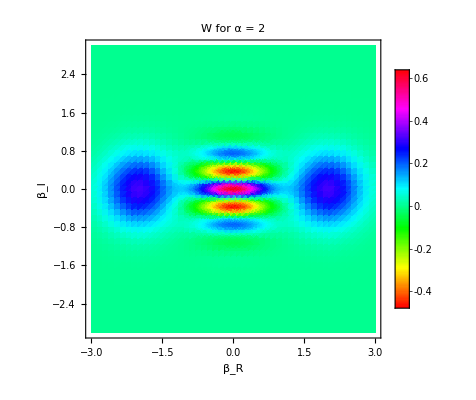

```mathematica
DensityPlot[W/.{αr->2,αi->0},{βr,-3,3},{βi,-3,3},PlotRange->{-1,1},
ColorFunction->Hue,PlotLegends->Automatic,PlotPoints->50,
FrameLabel->{"β_R","β_I"},
PlotLabel->"W for α = 2"]
```

```mathematica
Plot3D[W/.{αr->2,αi->0},{βr,-3,3},{βi,-3,3},PlotRange->All,
ColorFunction->"SolarColors",PlotLegends->Automatic,
PlotPoints->40,
ViewPoint->{1.3,-1.,0.1}]
```

-Graphics3D-